```mathematica
SetDirectory[NotebookDirectory[]]
wp = Import["eigfun/h2o2/normal_modes/wavepacket_chn.out", "Table"];
NP = 61;
NT=51;
DX=360/NP;
DT=0.1;
toffset=7.3;
INTERPOL=1;
l=0;
wavepacket = Table[ {toffset+wp[[i,2]],wp[[i,1]],wp[[i,3]]},{i,1,NP*NT}];
wpi=Table[{0,0,0},{i,1,NT*NP*INTERPOL}];
frame=Table[{0,0,0},{i,1,NT*NP*INTERPOL}];
Do[
   Do[ 
     l=l+1; 
     frame[[l]] = {DX*(k-0.5)/INTERPOL,DT*(j-1),0};
     wpi[[l]] = {DX*(k-0.5)/INTERPOL,DT*(j-1),Interpolation[wp[[(j-1)*NP+1;;j*NP,5]]][1+(k-1)/INTERPOL]}
     ,{k,1,INTERPOL*(NP-1)+1}]
    ,{j,1,NT,3}]
(*wavepacket = Table[ {wp[[i,2]],wp[[i,1]],wp[[i,3]]},{i,1,NP*NT}];*)
```

/Users/prentner/Mathematica notebooks/Molecular QD

0.086

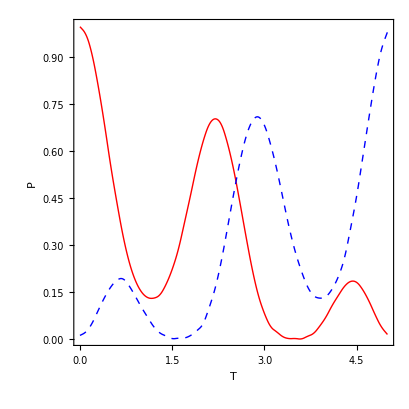

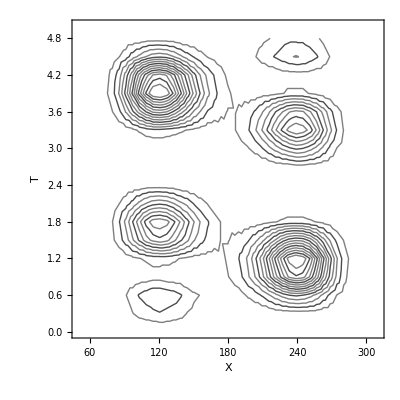

```mathematica
maxz=Max[wpi[[1;;NT*NP,3]]]
(*determine how much of the probability is ins left/right half of potential *)
pL=Table[{DT*(t-1),Sum[wp[[(t-1)*NP+j,3]],{j,1,0.5*(NP+1)}]},{t,1,NT}];
pR=Table[{DT*(t-1),Sum[wp[[(t-1)*NP+j,3]],{j,0.5*(NP-1),NP}]},{t,1,NT}];
ListLinePlot[{pL,pR},Frame->True,FrameLabel->{"T","P"},
PlotRange->{All,{0,1}},PlotStyle->{Directive[Red,Thick],Directive[Blue,Dashed,Thick]},
AspectRatio->1,InterpolationOrder->2,LabelStyle->Directive[FontFamily->"Times",FontSize->14]]
(*_-_-_-_*)
ListContourPlot[wpi,ColorFunctionScaling->True,ColorFunction->"TemperatureMap",ContourShading->None,InterpolationOrder->3,PlotRange->{{50,310},{0,5},{0.002,maxz}},FrameLabel->{"X","T"},ContourStyle->{Opacity[0.5],Opacity[0.7],Black},Contours->15,ImageSize->400,LabelStyle->Directive[FontFamily->"Times",FontSize->20]]
```

```mathematica
ListPlot3D[wpi,
Mesh->{31,31},MeshStyle->{Thickness[0.001],Thickness[0.001]},
PlotRange->{{50,310},{0,5.},{-0.0,0.15}},PerformanceGoal->Quality,ImageSize->500,BoxRatios->{0.75,1.1,0.25},LabelStyle->Directive[FontFamily->"Times",FontSize->20],Boxed->False,AxesEdge->{{0,0.},{1,0},{0,0}},ViewPoint->{3,-4.8,3},PlotTheme->"Classic"]
```

-Graphics3D-